# A 1D Random Walk with Unequal Probabilities of Left and Right Motion

## Milan Cvitkovic

## Section 01. Introduction

In a standard 1D random walk the probability of moving right, p, is equal to the probability of moving left, q, such that q = p = 0.5.  In this simulation, however, we will be looking at cases in which p and q are not equal (though obviously still summing to 1) and observing the effect this has on E[X_N], the expected position of a random walker after N steps (X_N is a random variable corresponding to the position of a random walker after N steps, E[y] is the expexted value of y).  More specifically, we will be trying to use our experimental data to derive a linear function which will give E[X_N] for a particular value of p.

## Section 02. Needed Packages

## Section 03. Statistical Functions

```mathematica
Clear[ave]
ave[List_] := Apply[Plus,List]/Length[List]
```

```mathematica
myList = {a,b,c,d}
```

{a,b,c,d}

```mathematica
ave[myList]
```

1/4 (a+b+c+d)

## Section 04. Code for a Single p Value

### Code for a Single X_N Run

```mathematica
Clear[steps]
steps[n_,p_] := 2Table[Floor[1+p-RandomReal[]],{n}]-1
```

```mathematica
steps[20,.5]
steps[20,.1]
steps[20,0]
```

{1,-1,-1,1,1,1,-1,1,-1,1,-1,1,1,1,1,-1,1,1,1,1}

{-1,-1,-1,-1,-1,1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
Clear[xValues]
xValues[n_,p_]:= FoldList[Plus,0,steps[n,p]]
```

```mathematica
xValues[20,.5]
xValues[20,.1]
xValues[20,0]
```

{0,1,2,1,2,3,2,3,4,3,4,3,4,3,4,3,4,5,6,5,4}

{0,-1,-2,-3,-4,-5,-6,-7,-8,-9,-10,-11,-12,-13,-14,-15,-16,-17,-16,-17,-18}

{0,-1,-2,-3,-4,-5,-6,-7,-8,-9,-10,-11,-12,-13,-14,-15,-16,-17,-18,-19,-20}

```mathematica
Clear[x]
x[n_,p_]:= Last[xValues[n,p]]
```

```mathematica
x[20,.5]
x[20,.1]
x[20,0]
```

4

-12

-20

### Code for an Ensemble of X_N Values

```mathematica
Clear[ensembleX]
ensembleX[n_,p_,numSamples_] := Table[N[x[n,p]],{numSamples}]
```

```mathematica
ensembleX[20,.5,10]
ensembleX[20,.1,10]
ensembleX[20,0,10]
```

{-4.,2.,-4.,-4.,6.,4.,2.,-2.,2.,4.}

{-18.,-18.,-18.,-16.,-16.,-12.,-14.,-16.,-18.,-10.}

{-20.,-20.,-20.,-20.,-20.,-20.,-20.,-20.,-20.,-20.}

### Code for an Ensemble Average for the Final Positions

```mathematica
Clear[findEnsembleAve]
findEnsembleAve[n_,p_,numSamples_] := 
	Module[{ensembleValues},
	ensembleValues = ensembleX[n,p,numSamples];
	{p,ave[ensembleValues]}
	];
```

```mathematica
findEnsembleAve[20,.5,10]
findEnsembleAve[20,.1,10]
findEnsembleAve[20,0,10]
```

{0.5,-1.4}

{0.1,-17.}

{0,-20.}

## Section 05. Results for a Range of p Values

### Table of Values

```mathematica
n = 1000
p=0.1
numTrials = 1000
aveTable = {}
While[p≤0.9,
(AppendTo[aveTable,findEnsembleAve[n,p,numTrials]];
p+=0.1;
)];
aveTable
```

1000

0.1

1000

{}

{{0.1,-800.28},{0.2,-598.666},{0.3,-401.064},{0.4,-199.606},{0.5,-1.724},{0.6,200.672},{0.7,399.062},{0.8,601.524},{0.9,800.58}}

### Plot of E[X_N]

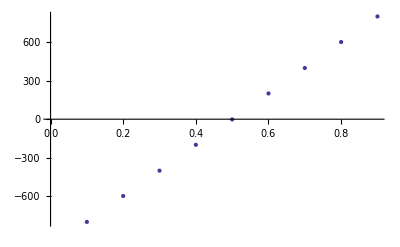

```mathematica
ListPlot[aveTable]
```

### Linear fit to a+bp

```mathematica
aveTableValues = ReplaceAll[aveTable,Rule[{p_,ave_},ave]]
```

{-800.28,-598.666,-401.064,-199.606,-1.724,200.672,399.062,601.524,800.58}

```mathematica
Clear[p]
Fit[aveTableValues,{1,p},p]
```

-1000.32+200.076 p

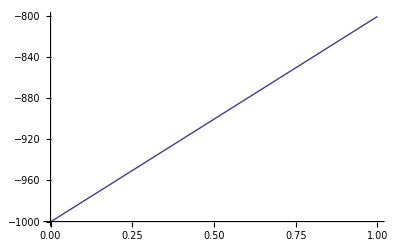

```mathematica
Plot[%,{p,0,1}]
```

```mathematica
Clear[p]
modelFit = LinearModelFit[aveTableValues,{1,p},p]
```

FittedModel[-1000.32+200.076 p]

```mathematica
modelFit["BestFit"]
```

-1000.32+200.076 p

```mathematica
modelFit["ParameterErrors"]
```

{0.85681,0.152259}